{surface0.gpl,surface1.gpl,surface2.gpl,surface3.gpl,surface4.gpl,surface5.gpl,surface6.gpl,surface7.gpl,surface8.gpl,surface9.gpl,surface10.gpl,surface11.gpl,surface12.gpl,surface13.gpl,surface14.gpl,surface15.gpl,surface16.gpl,surface17.gpl,surface18.gpl,surface19.gpl,surface20.gpl,surface21.gpl,surface22.gpl,surface23.gpl,surface24.gpl,surface25.gpl,surface26.gpl,surface27.gpl,surface28.gpl,surface29.gpl,surface30.gpl,surface31.gpl,surface32.gpl,surface33.gpl,surface34.gpl,surface35.gpl,surface36.gpl,surface37.gpl,surface38.gpl,surface39.gpl,surface40.gpl,surface41.gpl,surface42.gpl,surface43.gpl,surface44.gpl,surface45.gpl,surface46.gpl,surface47.gpl,surface48.gpl,surface49.gpl,surface50.gpl,surface51.gpl,surface52.gpl,surface53.gpl,surface54.gpl,surface55.gpl,surface56.gpl,surface57.gpl,surface58.gpl,surface59.gpl,surface60.gpl,surface61.gpl,surface62.gpl,surface63.gpl,surface64.gpl,surface65.gpl,surface66.gpl,surface67.gpl,surface68.gpl,surface69.gpl,surface70.gpl,surface71.gpl,surface72.gpl,surface73.gpl,surface74.gpl,surface75.gpl,surface76.gpl,surface77.gpl,surface78.gpl,surface79.gpl,surface80.gpl,surface81.gpl,surface82.gpl,surface83.gpl,surface84.gpl,surface85.gpl,surface86.gpl,surface87.gpl,surface88.gpl,surface89.gpl,surface90.gpl,surface91.gpl,surface92.gpl,surface93.gpl,surface94.gpl,surface95.gpl}

/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion

{{50,818509},{60,794578},{70,803157},{80,798431},{90,763262},{100,737287},{110,712753},{120,691482},{130,652616},{140,686645},{150,704552},{160,678610},{170,-922256},{180,633009},{190,-1.0651×10^7},{200,613590},{210,595752},{220,555390},{230,577473},{240,577620},{250,572102},{260,577428},{270,567435},{280,599516},{290,574892},{300,598486},{310,579847},{320,584886},{330,590380},{340,623085},{350,1.31101×10^6},{360,821830},{370,589284},{380,571430},{390,560056},{400,481942},{410,481996},{420,441447},{430,448401},{440,450747},{450,441574},{460,443911},{470,444424},{480,439870},{490,442212},{500,445294},{510,1.37072×10^7},{520,448556},{530,467292},{540,446932},{550,462077},{560,451398},{570,447809},{580,439084},{590,434193},{600,477023},{610,458389},{620,465926},{630,448735},{640,447198},{650,434107},{660,431770},{670,444123},{680,438159},{690,449866},{700,450549},{710,444870},{720,449677},{730,449066},{740,456200},{750,409723},{760,777618},{770,449432},{780,574743},{790,1.20997×10^6},{800,449056},{810,441543},{820,433386},{830,433768},{840,442676},{850,460732},{860,456931},{870,455036},{880,-140592},{890,466658},{900,459698},{910,440419},{920,453254},{930,453029},{940,452903},{950,448134},{960,456161},{970,457164},{980,458310},{990,452053},{1000,518612}}

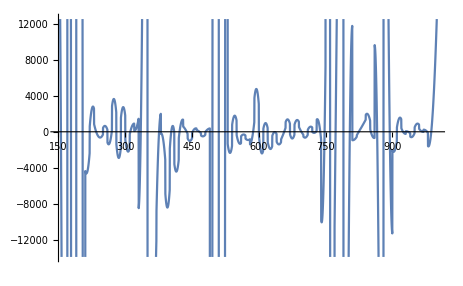

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion/gpls"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange -> All];
{plot1,plot2}
]
files= FileNames[];
(*Print[files]*)
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
ListAnimate[allPlots]
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
]
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion"]
Print[SolveForce["energysep.txt"]]
energysepfunc = Interpolation[SolveForce["energysep.txt"]];
forcefunction = energysepfunc';
Plot[forcefunction[x], {x, 150, 1000}]
```

```mathematica
(*{{150,10986.7},{165,11199.5},{180,11312.1},{195,11468.1},{210,11645.7},{225,11821.2},{240,12000},{255,12148.8},{270,12272.7},{285,12448.1},{300,12594.9},{315,12717.7},{330,12847.3},{345,12980.9},{360,13065.7},{375,13193.9},{390,13281.6},{405,13391.8},{420,13469.7},{435,13549.7},{450,13665.9},{465,13733.2},{480,13806.7},{495,13892.3},{510,13969.6},{525,14105.4},{540,14182.4},{555,14239},{570,14312.5},{585,14400.9},{600,14465.7},{615,14501.9},{630,14564.5},{645,14638.1},{660,14708.5},{675,14744.5},{690,14799.5},{705,14842.4},{720,14893.9},{735,14962.1},{750,14992.9},{765,15025.1},{780,15080.3},{795,15105.3},{810,15147.2},{825,15182.3},{840,15205},{855,15269.1},{870,15265.1},{885,15299.6},{900,15355.2},{915,15368.2},{930,15388.2},{945,15418.5},{960,15438},{975,15471},{990,15501.4}}*)
```